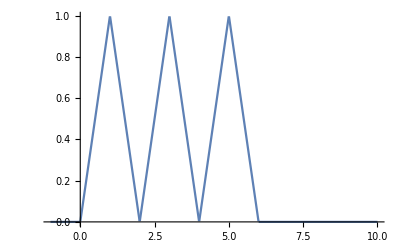

```mathematica
r[x_] := HeavisideTheta[x]*x
Plot[r[x] - 2r[x-1] + 2r[x-2] - 2r[x-3] + 2r[x-4] - 2r[x-5] + r[x-6], {x, -1, 10}]
```

```mathematica
Manipulate[Plot[1/(2a)(1 - Cos[a*π*x]) + (1 - a)x, {x, -1, 10}, PlotRange->{-15, 15}], {a, 0, 1}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
and[x_, y_] := x*y
or[x_, y_] := x + y - x*y

o1 = w1*a*b + (1 - w1)*(a + b - a*b);
o2 = w2*c*d + (1 - w2)*(c + d - c*d);o3 = w3*o1*o2 + (1 - w3)*(o1 + o2 - o1*o2);

probabilisticOutput = w1*w2*w3*(a*b*c*d) + w1*w2*(1 - w3)*(a*b + c*d - a*b*c*d) + w1*(1 - w2)*w3*(a*b*(c + d - c*d)) + (1 - w1)*w2*w3*((a + b - a*b)*c*d) + w1*(1 - w2)*(1 - w3)*or[and[a, b], or[c, d]] + (1 - w1)*w2*(1 - w3)*or[or[a, b], and[c, d]] + (1 - w1)*(1 - w2)*w3*and[or[a, b], or[c, d]] + (1 - w1)*(1 - w2)*(1 - w3)*or[or[a, b], or[c, d]]
probabilisticOutput - o3 // FullSimplify
```

(a+b-a b+c+d-c d-(a+b-a b) (c+d-c d)) (1-w1) (1-w2) (1-w3)+(a b+c+d-c d-a b (c+d-c d)) w1 (1-w2) (1-w3)+(a+b-a b+c d-(a+b-a b) c d) (1-w1) w2 (1-w3)+(a b+c d-a b c d) w1 w2 (1-w3)+(a+b-a b) (c+d-c d) (1-w1) (1-w2) w3+a b (c+d-c d) w1 (1-w2) w3+(a+b-a b) c d (1-w1) w2 w3+a b c d w1 w2 w3

0

```mathematica
Plot3D[(x*(1 - y) + (1 - x)*y)^2 + .1*(x*y)^2, {x, 0, 1}, {y, 0, 1}]
```

-Graphics3D-

```mathematica
ϕ = (1 + Sqrt[5])/2;
f[x_] := β*x^ϕ
f'[f[x]]
```

1/2 (1+√5) β (x^(1/2 (1+√5)) β)^(-1+1/2 (1+√5))

```mathematica
Solve[f'[f[1]] == 1, β][[1]]
β = (β /. %)
```

{β→(1/2 (-1+√5))^(2/(1+√5))}

(1/2 (-1+√5))^(2/(1+√5))

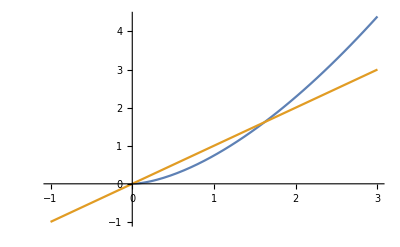

```mathematica
Plot[{f[x], x}, {x, -1, 3}]
```

```mathematica
1/ϕ // N
(1 - Sqrt[5])/2 // N
```

0.618034

-0.618034

```mathematica
q = 1;
f[x_] := q + a(x - q) + b(x - q)^2 + c(x - q)^3 + d(x - q)^4 + e(x - q)^5 + g(x - q)^6
Series[f'[f[x]] // Expand, {x, q, 6}]
eqns = {%[[3]][[1]] == q, %[[3]][[2]] == 1, %[[3]][[3]] == 0, %[[3]][[4]] == 0, %[[3]][[5]] == 0, %[[3]][[6]] == 0};
sols = NSolve[eqns, {a, b, c, d, e, g}][[1]]
```

a+2 a b (x-1)+(2 b^2+3 a^2 c) (x-1)^2+(2 b c+6 a b c+4 a^3 d) (x-1)^3+(3 b^2 c+6 a c^2+2 b d+12 a^2 b d+5 a^4 e) (x-1)^4+(6 b c^2+12 a b^2 d+6 a c d+12 a^2 c d+2 b e+20 a^3 b e+6 a^5 g) (x-1)^5+(3 c^3+4 b^3 d+6 b c d+24 a b c d+12 a^2 d^2+30 a^2 b^2 e+6 a c e+20 a^3 c e+2 b g+30 a^4 b g) (x-1)^6+O[x-1]^7

{a→1.,b→0.5,c→-0.166667,d→0.166667,e→-0.241667,g→0.429167}

```mathematica
f'[f[x + 2]] /. sols2 /. q->2 // Expand
```

2.+1. x-1.19262×10^-18 x^4-6.64074×10^-19 x^5+0.00259039 x^6+0.000713916 x^7+0.0000536688 x^8+5.79766×10^-7 x^9-1.47068×10^-7 x^10+5.47787×10^-8 x^11+2.47235×10^-8 x^12+1.10136×10^-9 x^13-2.04237×10^-11 x^14-3.32691×10^-13 x^15-2.71685×10^-13 x^16+4.60297×10^-13 x^17-7.31945×10^-15 x^18+4.33485×10^-16 x^19+1.18568×10^-17 x^20-1.98447×10^-17 x^21+6.74426×10^-18 x^22-6.39493×10^-19 x^23+6.74327×10^-20 x^24-6.83095×10^-21 x^25+5.83516×10^-22 x^26-3.34197×10^-23 x^27+2.16701×10^-24 x^28-1.19657×10^-25 x^29+4.19717×10^-27 x^30

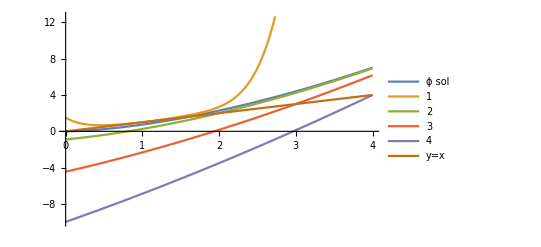

```mathematica
Clear[q]
Plot[{(1/ϕ)^(1/ϕ)x^ϕ, f[x] /. sols1 /. q->1, f[x] /. sols2 /. q->2, f[x] /. sols3 /. q->3, f[x] /. sols4 /. q->4, x}, {x, 0, 4}, PlotLegends->{"ϕ sol", "1", "2", "3", "4", "y=x"}]
```

```mathematica
sols1 = sols
```

{a→1.,b→0.5,c→-0.166667,d→0.166667,e→-0.241667,g→0.429167}

```mathematica
sols2 = sols
```

{a→2.,b→0.25,c→-0.0104167,d→0.00113932,e→-0.000169881,g→0.0000297944}

```mathematica
sols4 = sols
```

{a→4.,b→0.125,c→-0.000651042,d→8.26518×10^-6,e→-1.40692×10^-7,g→2.79808×10^-9}

```mathematica
sols3 = sols
```

{a→3.,b→0.166667,c→-0.00205761,d→0.0000635066,e→-2.63957×10^-6,g→1.28372×10^-7}

```mathematica
Γ = {{-1, 10}, {1, -10}};
MatrixExp[100*Γ] // N // MatrixForm
```

(0.909091 | 0.909091
0.0909091 | 0.0909091)

```mathematica
f[x_] := .1*x^2 - Cos[3x] + 1
q = .1;
Manipulate[
Plot[(α*f[x]^q + (1 - α)*f[x-3]^q), {x, -5, 8}, PlotRange->{0, 10}],
{α, 0, 1}
]
```